```mathematica
GLargeNfreal=-(ⅈ ⅇ^(-(Abs[x]^(1/3) Gamma[2/3])/(3 2^(2/3) √3 Nfkf^(1/3) π^(5/3) v^(4/3) (1/v+(ⅈ τ)/x)^(2/3))))/(2 π (x+ⅈ v τ));
```

```mathematica
GLargeNfOtherNotebook=-Cos[(ω √(ⅈ kxv+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkfv π^(5/2) (kxv-ⅈ ω)^2)]/(kxv-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkfv π^5 (ⅈ kxv+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkfv ω)^(1/3) (ⅈ kxv+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkfv π^5 (ⅈ kxv+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (kxv-ⅈ ω)^3 (Nfkfv ω)^(2/3));
```

```mathematica
GLargeNfOtherNotebookFixed=GLargeNfOtherNotebook/.{ω->-ω,kxv->-kx,Nfkfv->Nfkf}
```

-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3))

```mathematica
(-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3))/.{ω->-ω})*
```

Conjugate[-Cos[(ω √(-ⅈ kx+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx-ⅈ ω)^2)]/(-kx-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkf ω)^(1/3) (-ⅈ kx+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx-ⅈ ω)^3 (Nfkf ω)^(2/3))]

```mathematica
GLargeNfv1[ω_,kx_,Nfkf_]:=If[ω<0,-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3)),Conjugate[-Cos[(ω √(-ⅈ kx+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx-ⅈ ω)^2)]/(-kx-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkf ω)^(1/3) (-ⅈ kx+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx-ⅈ ω)^3 (Nfkf ω)^(2/3))]]
```

```mathematica
test={v->1,Nfkf->1,ω->-1,kx->-.3};
nint=GLargeNfreal Exp[-ⅈ ω τ+ⅈ kx x]/.test;
```

```mathematica
xint[τi_?NumericQ]:=NIntegrate[nint/.τ->τi,{x,-∞,0,∞},Method->"LevinRule",MaxRecursion->20, PrincipalValue->True]
τint[xi_?NumericQ]:=NIntegrate[nint/.x->xi,{τ,-∞,0,∞},Method->"LevinRule",MaxRecursion->20, PrincipalValue->True]
```

```mathematica
τs=Table[τi,{τi,-100,100,.1}];
vv=ParallelTable[xint[τi],{τi,τs}];
xintIP=Interpolation[{τs,vv}ᵀ];
```

```mathematica
xs=Table[xi,{xi,-50,50,.05}];
vv2=ParallelTable[τint[xi],{xi,xs}];
τintIP=Interpolation[{xs,vv2}ᵀ];
```

1
Power::infy: Infinite expression -- encountered.
                                 0.

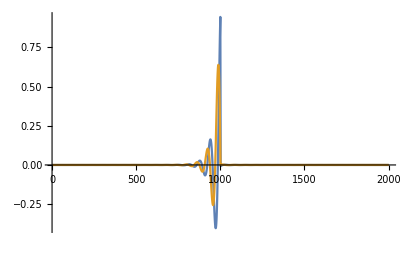

```mathematica
ListLinePlot[ReIm[vv]ᵀ,PlotRange->All]
```

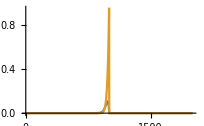

```mathematica
ListLinePlot[ReIm[vv2]ᵀ,PlotRange->All]
```

```mathematica
NIntegrate[τintIP[τ],{τ,-100,0,100},PrincipalValue->True]
```

0.261869+0.897254 ⅈ

```mathematica
NIntegrate[xintIP[τ],{τ,-100,0,100},PrincipalValue->True]
```

0.262176+0.896179 ⅈ

```mathematica
NIntegrate[xint[τi],{τi,-100,0,100},PrincipalValue->True]
```

0.261929+0.897006 ⅈ

```mathematica
test
```

{v→1,Nfkf→1,ω→-1,kx→-0.3}

```mathematica
GLargeNfv1[-1,-.3,1]
GLargeNfv1[-1,.3,1]
```

-0.261932-0.89704 ⅈ

0.261932-0.89704 ⅈ

```mathematica
Gf0[ω,kx]
```

1/(-kx v+ⅈ ω)

```mathematica
Gf0[-1,-.3]/.v->1
```

0.275229+0.917431 ⅈ

```mathematica
GLargeNfv1[ω,kx,1]/.test
```

-0.261932-0.89704 ⅈ

```mathematica
test
```

{v→1,Nfkf→1,ω→-1,kx→-0.3}

```mathematica
NumberForm[GLargeNf/.{Nfkfv->Nfkf v,kxv->kx v}/.{ω->ω,kx->kx}/.test,20]
NumberForm[GLargeNf/.{Nfkfv->Nfkf v,kxv->kx v}/.{ω->-ω,kx->-kx}/.test,20]
```

0.2505959122574448+0.918469802778155 ⅈ

-0.2619316746935476-0.897040376189872 ⅈ

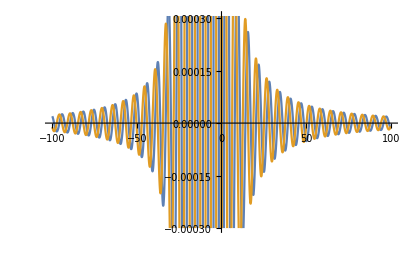

```mathematica
Plot[Evaluate@ReIm[xintIP[τ]],{τ,-100,100}]
```

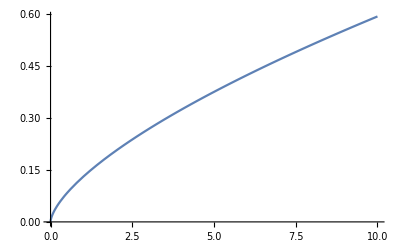

```mathematica
Plot[Im[1/GLargeNf-(-kxv+ⅈ ω)]/.{Nfkfv->1/100,kxv->0},{ω,0,10}]
```

```mathematica
Nfs={1/100,1/10,1};
ωm=10;
n=2^8;
ωs=Subdivide[-ωm,ωm,n-1];
Do[
f=OpenWrite[NotebookDirectory[]<>"benchmarkRefOutput/benchmarkRef2_Nf="<>ToString[N@Nfkfv],BinaryFormat->True];
BinaryWrite[f,n,"Integer32"];
BinaryWrite[f,ωm,"Real64"];
BinaryWrite[f,Flatten@ParallelTable[N[GLargeNf,40],{ω,ωs},{kxv,ωs}],"Complex128"];
Close[f];
,{Nfkfv,Nfs}]
```

```mathematica
Limit[GLargeNf,Nfkfv->∞]
```

1/(-kxv+ⅈ ω)

```mathematica
n=2^7;
ωs=Subdivide[-ωm,ωm,n-1];
bb=ParallelTable[N[GLargeNf/.Nfkfv->1/100,20],{ω,ωs},{kxv,ωs}];
```

```mathematica
n=2^7;
ωs=Subdivide[-ωm,ωm,n-1];
aa=ParallelTable[N[1/GLargeNf-(-kxv+ⅈ ω)/.Nfkfv->1/100,20],{ω,ωs},{kxv,ωs}];
```

```mathematica
ListPlot3D[Re[bb]]
```

-Graphics3D-

```mathematica
aa[[1,1]]
```

-0.50545762924729886453-0.2834131038166370972 ⅈ

```mathematica
ListPlot3D[Im[aa]]
```

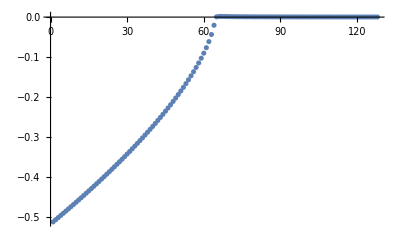

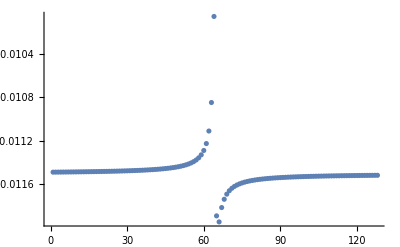

```mathematica
ListPlot[Re[aa[[;;,66]]]]
ListPlot[Im[aa[[64,;;]]],PlotRange->All]
```